```mathematica
Arms[x1_,x2_,x3_,x4_]:=FindRoot[
{Sum[Cos[Subscript[θ, i]],{i,1,4}]==1,
Sum[Sin[Subscript[θ, i]],{i,1,4}]==0,
Sum[Cos[Subscript[θ, i]+Sum[Subscript[δ, j],{j,1,i}]],{i,1,4}]==1,
Sum[Sin[Subscript[θ, i]+Sum[Subscript[δ, j],{j,1,i}]],{i,1,4}]==0},
{{Subscript[θ, 1],x1},{Subscript[θ, 2],x2},{Subscript[θ, 3],x3},{Subscript[θ, 4],x4}},
MaxIterations->1000]
TraceOut[x_,y_]:=FindRoot[
{Subscript[L, 1] Cos[Subscript[θ, 1]]+Subscript[L, 2] Cos[Subscript[θ, 2]]==x,
Subscript[L, 1] Sin[Subscript[θ, 1]]+Subscript[L, 2] Sin[Subscript[θ, 2]]==y
},
{{Subscript[θ, 1],0.1,-π,π},{Subscript[θ, 2],1.5,-π,π}}
]
```

```mathematica
Subscript[δ, 1]=-0.07420;Subscript[δ, 2]=0.07420;Subscript[δ, 3]=-0.04497;Subscript[δ, 4]=-0.00179;
sol=Arms[3,1,2,1] (*Set 1*)
```

{θ_1→1.88484,θ_2→0.628205,θ_3→5.65487,θ_4→-1.88514}

```mathematica
Subscript[δ, 1]=-0.07420;Subscript[δ, 2]=0.02742;Subscript[δ, 3]=0.02853;Subscript[δ, 4]=-0.07487;
sol=Arms[2,1,6,4] (*Set 2*)
```

{θ_1→1.8849,θ_2→0.628398,θ_3→5.65479,θ_4→4.39828}

```mathematica
Subscript[δ, 1]=-0.02412;Subscript[δ, 2]=-0.16026;Subscript[δ, 3]=0.27843;Subscript[δ, 4]=-0.27794;
sol=Arms[2,0.5,6,4] (*Set 3*)
```

{θ_1→1.88503,θ_2→0.628328,θ_3→5.6549,θ_4→4.39828}

```mathematica
Subscript[δ, 1]=0.07272;Subscript[δ, 2]=1.20678;Subscript[δ, 3]=4.78410;Subscript[δ, 4]=1.3022;
sol=Arms[2,0.5,6,4] (*Set 4*)
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{θ_1→1.06552,θ_2→-0.982549,θ_3→5.51952,θ_4→2.43605}

```mathematica
Subscript[δ, 1]=-0.71895;Subscript[δ, 2]=0.71895;Subscript[δ, 3]=-0.52670;Subscript[δ, 4]=-0.15747;
sol=Arms[2,0.5,6,4] (*Set 5*)
```

{θ_1→1.11641,θ_2→0.261798,θ_3→5.28677,θ_4→3.46502}

{{0,0},{0.438912,0.89853},{1.40484,1.15735},{1.94815,0.317818},{1.,1.11022×10^-16}}

{{0,0},{0.922048,0.387076},{1.88797,0.645894},{1.93563,-0.35297},{1.,1.11022×10^-16}}

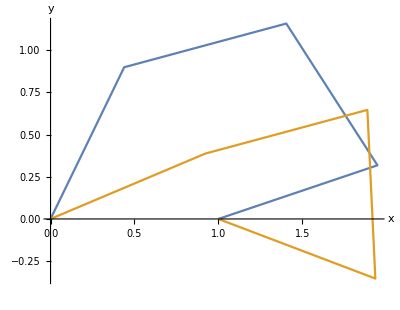

```mathematica
start = Prepend[Table[{Sum[Cos[Subscript[θ, i]]/.sol,{i,1,n}],Sum[Sin[Subscript[θ, i]]/.sol,{i,1,n}]},{n,1,4}],{0,0}]
end = Prepend[Table[{Sum[Cos[Subscript[θ, i]+Sum[Subscript[δ, j],{j,1,i}]]/.sol,{i,1,n}],Sum[Sin[Subscript[θ, i]+Sum[Subscript[δ, j],{j,1,i}]]/.sol,{i,1,n}]},{n,1,4}],{0,0}]
ListPlot[{start,end}, Joined->True,AspectRatio->Automatic,AxesLabel->{"x","y"}]
```

```mathematica
p12={};
Do[{
ans=TraceOut[d[[a]][[1]],d[[a]][[2]]];
If[(Abs[Sum[Subscript[L, i] Cos[Subscript[θ, i]]/.ans,{i,1,2}]-d[[a]][[1]]]>10^-4 ||Abs[Sum[Subscript[L, i] Sin[Subscript[θ, i]],{i,1,2}]-d[[a]][[2]]]>10^-4)||(((des/.ans)>0)&&((t/.tsol[[1]]/.ans)<1)),AppendTo[p12,{d[[a]][[1]],d[[a]][[2]]}]]
},{a,1,Length[d]}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

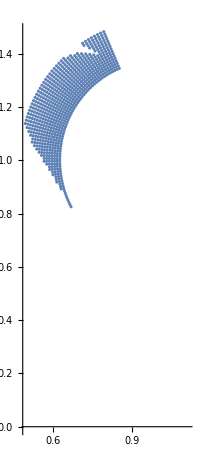

```mathematica
ListPlot[{p12},AspectRatio->Automatic]
```

```mathematica
Complement[d,p12]
```

{}

```mathematica
Export["Long.dat",Union[Complement[d,p11],Complement[d,p12]]]
```

Long.dat

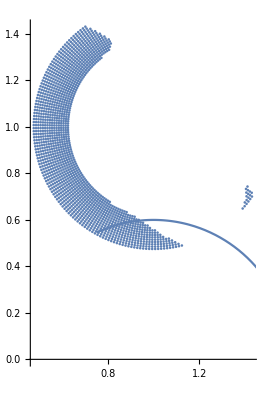

```mathematica
Show[ListPlot[Union[Complement[d,p11],Complement[d,p12]],AspectRatio->Automatic],
ParametricPlot[{1+0.6Cos[t],0.6Sin[t]},{t,0,2}]]
```

```mathematica
Export["Bottom4.dat",p11]
```

Bottom4.dat

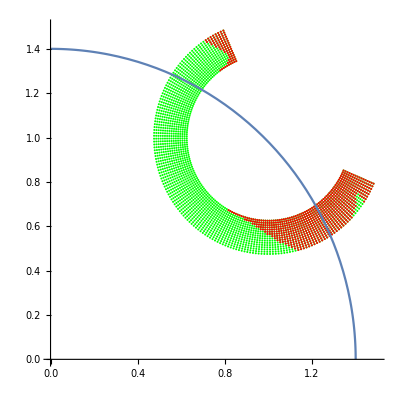

```mathematica
Show[ListPlot[{d,p11},PlotRange->{{0,1.5},{0,1.5}},AspectRatio->Automatic,PlotStyle->{Green,Red}],
ParametricPlot[{1.4Cos[t],1.4Sin[t]},{t,0,π/2}]]
```

```mathematica
Subscript[L, 1]=5/5
Subscript[L, 2]=600/1000
```

1

3/5

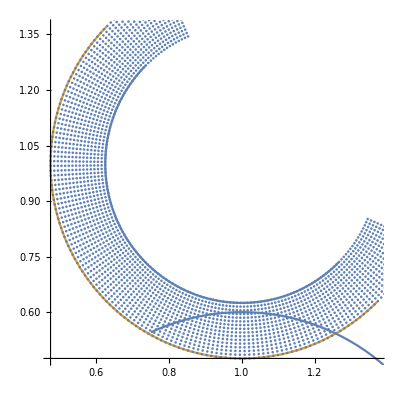

```mathematica
d=ArrayReshape[Table[{1+r Cos[t],1+r Sin[t]},{r,0.375,0.525,0.01},{t,3 π/4-0.38,7 π/4+0.38,0.025}],{16 157,2}];
Show[ParametricPlot[{{1+0.375Cos[2π t],1+0.375Sin[2π t]},{1+0.525Cos[2π t],1+0.525Sin[2π t]}},{t,3/8,7/8}],ListPlot[{d,p11},AspectRatio->Automatic],
ParametricPlot[{1+0.6Cos[t],0.6Sin[t]},{t,0,2}]]
```

```mathematica
TraceOut[d[[1]][[1]],d[[1]][[2]]]
```

{θ_1→1.6562,θ_2→0.355702}

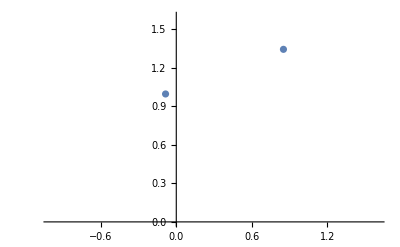

```mathematica
ListPlot[{{Cos[1.6562],Sin[1.6562]},{Cos[0.355]+Cos[1.6562],Sin[0.355]+Sin[1.6562]}},PlotRange->{{-1,1.6},{0,1.6}}]
```

```mathematica
Norm[d[[1]]]
```

1.59187

```mathematica
Export["Total.dat",d]
```

Total.dat

```mathematica
N[ArcTan[1/55 (64+3 √119)]]
```

1.05377

```mathematica
Export["Lower.dat",q]
```

Lower.dat

```mathematica
tsol=Simplify[Solve[Collect[Expand[(Subscript[L, 1] Cos[Subscript[θ, 1]]+Subscript[L, 2] Cos[Subscript[θ, 2]]t-1)^2+(Subscript[L, 1] Sin[Subscript[θ, 1]]+Subscript[L, 2] Sin[Subscript[θ, 2]]t-1)^2-(375/1000)^2==0],t],t]]
```

{{t→-5/24 (8 Cos[θ_1-θ_2]-8 Cos[θ_2]-8 Sin[θ_2]+√(-87+64 Cos[θ_1]-64 Cos[θ_1-2 θ_2]+32 Cos[2 (θ_1-θ_2)]+64 Sin[θ_1]+64 Sin[θ_1-2 θ_2]+64 Sin[2 θ_2]))},{t→5/24 (-8 Cos[θ_1-θ_2]+8 Cos[θ_2]+8 Sin[θ_2]+√(-87+64 Cos[θ_1]-64 Cos[θ_1-2 θ_2]+32 Cos[2 (θ_1-θ_2)]+64 Sin[θ_1]+64 Sin[θ_1-2 θ_2]+64 Sin[2 θ_2]))}}

```mathematica
des=-87+64 Cos[Subscript[θ, 1]]-64 Cos[Subscript[θ, 1]-2 Subscript[θ, 2]]+32 Cos[2 (Subscript[θ, 1]-Subscript[θ, 2])]+64 Sin[Subscript[θ, 1]]+64 Sin[Subscript[θ, 1]-2 Subscript[θ, 2]]+64 Sin[2 Subscript[θ, 2]]
```

-87+64 Cos[θ_1]-64 Cos[θ_1-2 θ_2]+32 Cos[2 (θ_1-θ_2)]+64 Sin[θ_1]+64 Sin[θ_1-2 θ_2]+64 Sin[2 θ_2]

```mathematica
Subscript[L, a] Sin[Subscript[θ, 1]]Sum[Subscript[ϕ, i],{i,1,1}]+Subscript[L, b] Sin[Subscript[θ, 2]]Sum[Subscript[ϕ, i],{i,1,2}]+Subscript[L, c] Sin[Subscript[θ, 3]]Sum[Subscript[ϕ, i],{i,1,3}]
```

Sin[θ_1] L_a ϕ_1+Sin[θ_2] L_b (ϕ_1+ϕ_2)+Sin[θ_3] L_c (ϕ_1+ϕ_2+ϕ_3)

```mathematica
Simplify[Expand[(Sin[Subscript[θ, 1]] Subscript[L, a] Subscript[ϕ, 1]+Sin[Subscript[θ, 2]] Subscript[L, b] (Subscript[ϕ, 1]+Subscript[ϕ, 2])+Sin[Subscript[θ, 3]] Subscript[L, c] (Subscript[ϕ, 1]+Subscript[ϕ, 2]+Subscript[ϕ, 3]))^2+(Cos[Subscript[θ, 1]] Subscript[L, a] Subscript[ϕ, 1]+Cos[Subscript[θ, 2]] Subscript[L, b] (Subscript[ϕ, 1]+Subscript[ϕ, 2])+Cos[Subscript[θ, 3]] Subscript[L, c] (Subscript[ϕ, 1]+Subscript[ϕ, 2]+Subscript[ϕ, 3]))^2]]
```

L_a^2 ϕ_1^2+L_b^2 (ϕ_1+ϕ_2)^2+2 Cos[θ_2-θ_3] L_b L_c (ϕ_1+ϕ_2) (ϕ_1+ϕ_2+ϕ_3)+L_c^2 (ϕ_1+ϕ_2+ϕ_3)^2+2 L_a ϕ_1 (Cos[θ_1-θ_2] L_b (ϕ_1+ϕ_2)+Cos[θ_1-θ_3] L_c (ϕ_1+ϕ_2+ϕ_3))

```mathematica
Simplify[Subscript[L, a]^2 Subscript[ϕ, 1]^2+Subscript[L, b]^2 (Subscript[ϕ, 1]+Subscript[ϕ, 2])^2+2  Subscript[L, b] Subscript[L, c] (Subscript[ϕ, 1]+Subscript[ϕ, 2]) (Subscript[ϕ, 1]+Subscript[ϕ, 2]+Subscript[ϕ, 3])+Subscript[L, c]^2 (Subscript[ϕ, 1]+Subscript[ϕ, 2]+Subscript[ϕ, 3])^2+2 Subscript[L, a] Subscript[ϕ, 1] (Subscript[L, b] (Subscript[ϕ, 1]+Subscript[ϕ, 2])+ Subscript[L, c] (Subscript[ϕ, 1]+Subscript[ϕ, 2]+Subscript[ϕ, 3]))]
```

(L_a ϕ_1+L_b (ϕ_1+ϕ_2)+L_c (ϕ_1+ϕ_2+ϕ_3))^2

```mathematica
Solve[Subscript[L, a] Subscript[ϕ, 1]+Subscript[L, b] (Subscript[ϕ, 1]+2 Subscript[ϕ, 1])+Subscript[L, c] (Subscript[ϕ, 1]+2 Subscript[ϕ, 1]+4 Subscript[ϕ, 1])==T,
Subscript[ϕ, 1]]
```

{{ϕ_1→T/(L_a+3 L_b+7 L_c)}}

```mathematica
0.0127/(1+3 0.4+7 0.4)
```

0.00254

```mathematica
Solve[Subscript[L, a] Subscript[ϕ, 1]+Subscript[L, b] (Subscript[ϕ, 1]+2 Subscript[ϕ, 1])+Subscript[L, c] (Subscript[ϕ, 1]+2 Subscript[ϕ, 1]+4 Subscript[ϕ, 1])==T,
Subscript[ϕ, 1]]
```

```mathematica
sol=Minimize[{1/Subscript[ϕ, 1]+1/Subscript[ϕ, 2]+1/Subscript[ϕ, 3], Subscript[ϕ, 1]+2/5 (Subscript[ϕ, 1]+Subscript[ϕ, 2])+2/5 (Subscript[ϕ, 1]+Subscript[ϕ, 2]+Subscript[ϕ, 3])<0.0127,Subscript[ϕ, 1]>0, Subscript[ϕ, 2]>0,Subscript[ϕ, 3]>0},{Subscript[ϕ, 1],Subscript[ϕ, 2],Subscript[ϕ, 3]}∈Reals];
```

NMinimize::incst: NMinimize was unable to generate any initial points satisfying the inequality constraints {-0.0127+(9 ϕ_1)/5+(4 ϕ_2)/5+(2 ϕ_3)/5≤0}. The initial region specified may not contain any feasible points. Changing the initial region or specifying explicit initial points may provide a better solution.

```mathematica
N[Subscript[ϕ, 2]/Subscript[ϕ, 1]/.sol[[2]]]
N[Subscript[ϕ, 3]/Subscript[ϕ, 1]/.sol[[2]]]
N[Subscript[ϕ, 1]/.sol[[2]]]
```

1.5

2.12132

0.00329996